# Домашнее задание №6, Широков Александр, ПМ-1701

## Set Covering Formulation

## 1.1 Постановка задачи

## 1.2 Тестовый пример

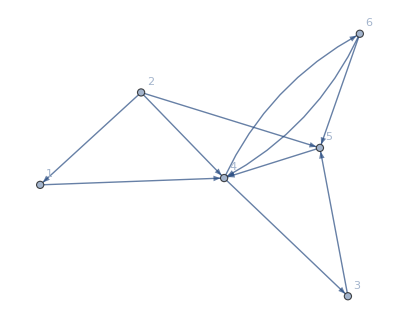

```mathematica
gr=RandomGraph[{6,10},DirectedEdges->True,VertexLabels->"Name"]
```

Ищем циклы в графе

```mathematica
cycles=FindCycle[gr,Infinity,All];
A=EdgeList[gr];
```

Матрица M размерности (n ×c )

```mathematica
M=SparseArray@Table[a=ConstantArray[0,Length[A]];a⟦EdgeIndex[gr,c]⟧=1;a,{c,cycles}]
```

SparseArray[…]

Переменные y

```mathematica
vars=y/@EdgeList[gr]
```

{y[1->4],y[2->1],y[2->4],y[2->5],y[3->5],y[4->3],y[4->6],y[5->4],y[6->4],y[6->5]}

Objective Function

```mathematica
W=Range[1,10];
objfun=Total[vars*W];
```

Коэффициенты целевой функции

```mathematica
c=Last[CoefficientArrays[objfun,vars]]
```

SparseArray[…]

Ограничения правой части

```mathematica
b=ConstantArray[{1,1},Length@cycles];
```

Множество принадлежности чисел

```mathematica
domain=ConstantArray[Integers,Length[vars]];
```

Интервалы, в которых могут применять значения неизвестные

```mathematica
lu=ConstantArray[{0,1},Length[vars]];
```

```mathematica
solution=Quiet[LinearProgramming[c, M, b, lu, domain]]
```

{0,0,0,0,1,0,1,0,0,0}

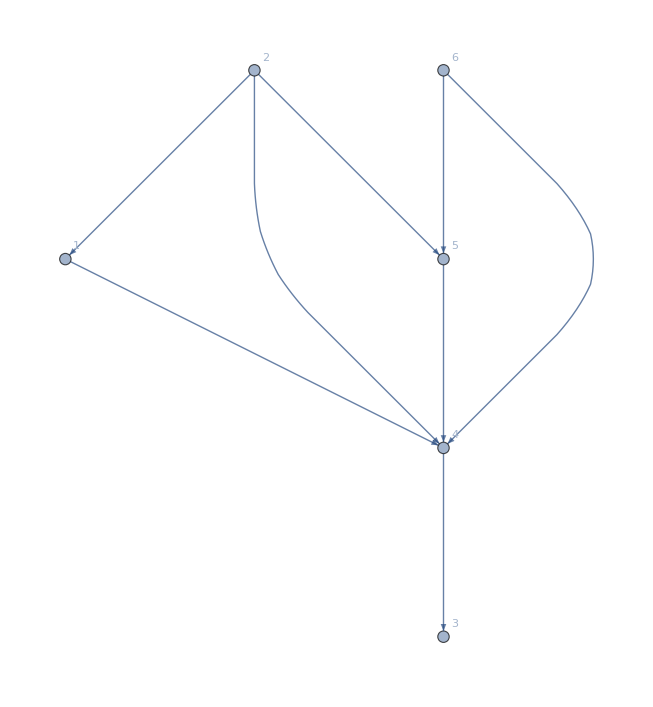

```mathematica
setCoveringFormulationSolution=Graph[Pick[A,solution,0],DirectedEdges->True,VertexLabels->"Name"]
```

## 1.3 Реализация

```mathematica
SetCoveringFormulation[g_?GraphQ,W_]:=Module[{cycles,A,M,a,vars,objfun,c,b,domain,lu,solution,setCoveringFormulationSolution},
cycles=FindCycle[g,Infinity,All];
A=EdgeList[g];
M=SparseArray@Table[a=ConstantArray[0,Length[A]];a⟦EdgeIndex[g,c]⟧=1;a,{c,cycles}];
vars=y/@EdgeList[g];
objfun=Total[vars*W];
c=Last[CoefficientArrays[objfun,vars]];b=ConstantArray[{1,1},Length@cycles];domain=ConstantArray[Integers,Length[vars]];lu=ConstantArray[{0,1},Length[vars]];solution=Quiet[LinearProgramming[c, M, b, lu, domain]];
setCoveringFormulationSolution=Graph[Pick[A,solution,0],DirectedEdges->True,VertexLabels->"Name"]]
```

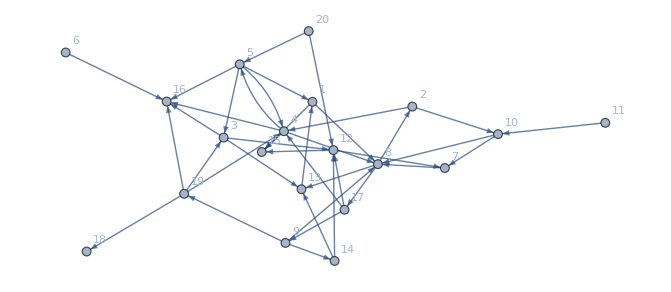

```mathematica
v=20;
e=40;
g=RandomGraph[{v,e},DirectedEdges->True,VertexLabels->"Name"]
```

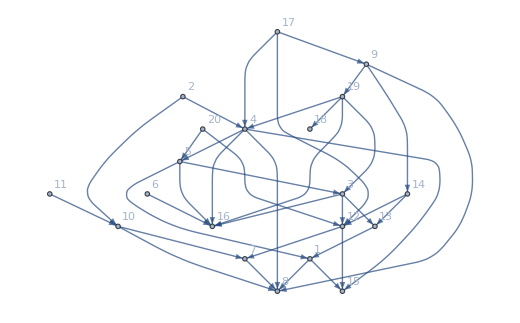

```mathematica
SetCoveringFormulation[g, ConstantArray[1,e]]
```

## Неравенство Треугольника

## 2.1 Постановка задачи

## 2.2 Тестовый пример

```mathematica
Clear[a,r,b,x]
```

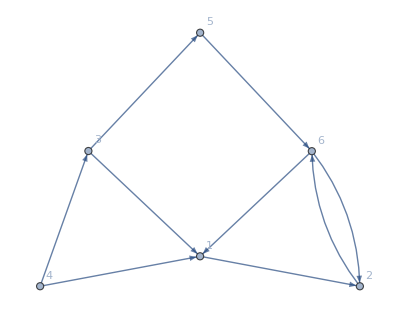

{1,2,6,3,5,4}

{1->2,2->6,3->1,3->5,4->1,4->3,5->6,6->1,6->2}

{2,10,6,2,9,3,10,5,4}

```mathematica
g=Graph[{1->2,2->6,3->1,3->5,4->1,4->3,5->6,6->1,6->2},DirectedEdges->True,VertexLabels->"Name"]
vertes=VertexList[g]
edges=EdgeList[g]
W = RandomInteger[{0,10},Length@edges]
```

Свяжем ассоциациями ребра и веса

```mathematica
as=Association[Thread[edges->W]]
```

<|1->2→2,2->6→10,3->1→6,3->5→2,4->1→9,4->3→3,5->6→10,6->1→5,6->2→4|>

Составим матрицу C

```mathematica
c=Table[If[MemberQ[edges,i->j],as⟦Key[i->j]⟧,0],{i,Length@vertes},{j,Length@vertes}];
Normal@c//MatrixForm
```

(0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 10
6 | 0 | 0 | 0 | 2 | 0
9 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 10
5 | 4 | 0 | 0 | 0 | 0)

Первая сумма: берем все дуги, в которых левая вершина больше правой

```mathematica
obj1=Total@Table[c⟦Last[e],First[e]⟧*e,{e,x@@@Cases[edges,a_->r_/;a>r->{a,r}]}]
```

10 x[6,2]

Вторая сумма: берем все дуги, в которых левая вершина меньше левой

```mathematica
obj2=Total@Table[c⟦First[e],Last[e]⟧*(1-e),{e,x@@@Cases[edges,a_->r_/;a<r->{a,r}]}]
```

2 (1-x[1,2])+10 (1-x[2,6])+2 (1-x[3,5])+10 (1-x[5,6])

```mathematica
objfun=obj1+obj2
```

2 (1-x[1,2])+10 (1-x[2,6])+2 (1-x[3,5])+10 (1-x[5,6])+10 x[6,2]

Переменные

```mathematica
varsX=x@@@edges
```

{x[1,2],x[2,6],x[3,1],x[3,5],x[4,1],x[4,3],x[5,6],x[6,1],x[6,2]}

Условие - неравенство треугольника

```mathematica
Clear[triangle];
triangle[{i_,j_,k_}]:=If[First[i]==First[k]&&Last[i]==First[j]&&Last[j]==Last[k],{{i+j-k,{1,-1}},{i+j-k,{0,1}}},Nothing]
cond=Flatten[triangle/@Permutations[varsX,{3}],1]
```

{{x[3,1]-x[4,1]+x[4,3],{1,-1}},{x[3,1]-x[4,1]+x[4,3],{0,1}},{x[1,2]+x[6,1]-x[6,2],{1,-1}},{x[1,2]+x[6,1]-x[6,2],{0,1}}}

Получаем решение

```mathematica
c=Last[CoefficientArrays[objfun,varsX]];
b=cond⟦All,2⟧;
m=Last[CoefficientArrays[cond⟦All,1⟧,varsX]];
lu=ConstantArray[{0,1},Length[varsX]];
domain=ConstantArray[Integers,Length[varsX]];
solution=Quiet[LinearProgramming[c,m,b,lu,domain]]
```

{1,1,0,1,0,0,1,0,0}

Исходный граф

```mathematica
g
```

-Graphics-

Возьмем единицы

{x[1,2],x[2,6],x[3,5],x[5,6]}

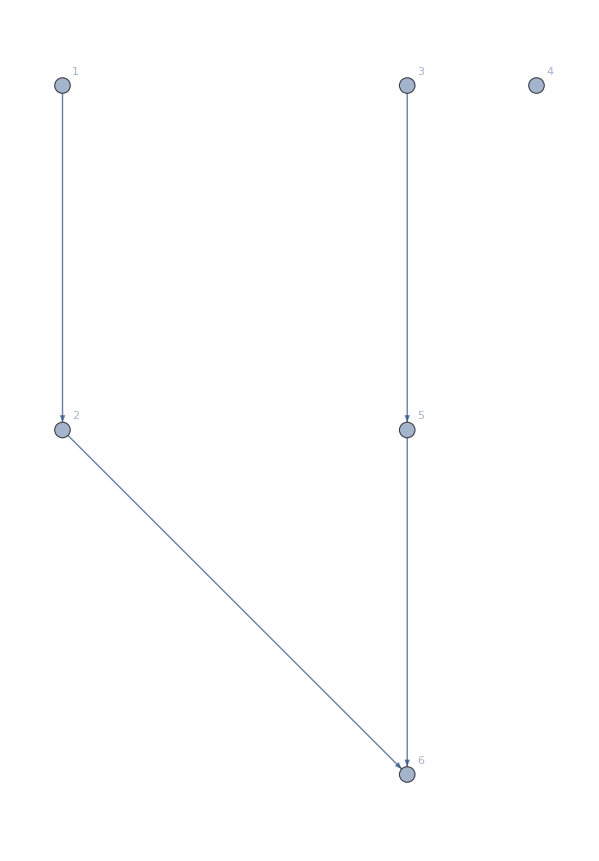

```mathematica
vResult=Pick[varsX,solution,1]
resultGraph =Graph[Table[{First[t],Last[t]},{t,vResult}],DirectedEdges->True,VertexLabels->"Name"];
resultGraph
```

## 2.3 Реализация

```mathematica
Clear[triangle];
triangle[{i_,j_,k_}]:=If[First[i]==First[k]&&Last[i]==First[j]&&Last[j]==Last[k],{{i+j-k,{1,-1}},{i+j-k,{0,1}}},Nothing]
```

```mathematica
Clear[getAcyclicTriangle]
getAcyclicTriangle[g_?GraphQ,W_]:=Module[{vertes=VertexList[g],edges=EdgeList[g],as,c,obj1,obj2,varsX,objfun,cond,b,m,lu,domain,solution,vResult,resultGraph },
as=Association[Thread[edges->W]];
c=Table[If[MemberQ[edges,i->j],as⟦Key[i->j]⟧,0],{i,Length@vertes},{j,Length@vertes}];
obj1=Total@Table[c⟦Last[e],First[e]⟧*e,{e,x@@@Cases[edges,a_->r_/;a>r->{a,r}]}];
obj2=Total@Table[c⟦First[e],Last[e]⟧*(1-e),{e,x@@@Cases[edges,a_->r_/;a<r->{a,r}]}];
(*varsX=Sort[x@@@Cases[Permutations[vertes,{2}],{a_,r_}/;a<r->{a,r}]]*);
varsX=x@@@edges;
objfun=obj1+obj2;
cond=Flatten[triangle/@Permutations[varsX,{3}],1];
c=Last[CoefficientArrays[objfun,varsX]];
b=cond⟦All,2⟧;
m=Last[CoefficientArrays[cond⟦All,1⟧,varsX]];
lu=ConstantArray[{0,1},Length[varsX]];
domain=ConstantArray[Integers,Length[varsX]];
solution=Quiet[LinearProgramming[c,m,b,lu,domain]];
vResult=Pick[varsX,solution,1];
resultGraph =Graph[Table[{First[t],Last[t]},{t,vResult}],DirectedEdges->True,VertexLabels->"Name"];
resultGraph
]
```

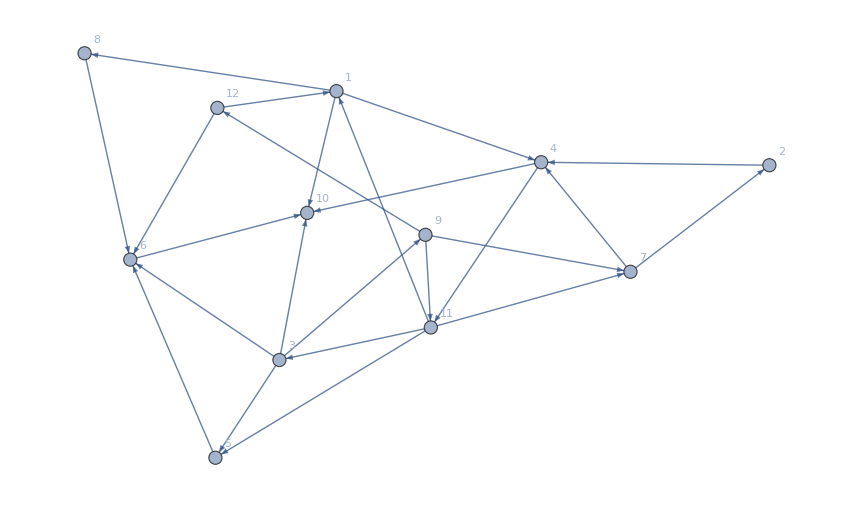

```mathematica
v=12;
e=24;
g=RandomGraph[{v,e},DirectedEdges->True,VertexLabels->"Name"]
W=RandomInteger[{0,7},e];
```

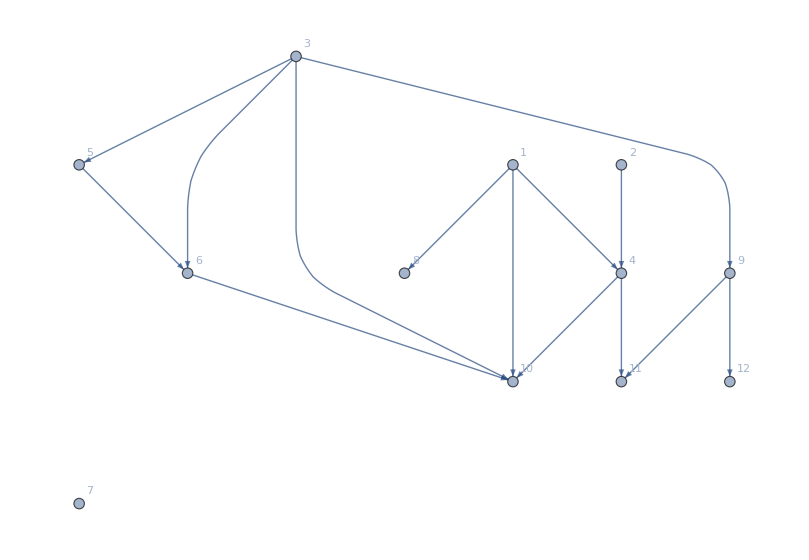

```mathematica
getAcyclicTriangle[g,W]
```